# Heaviside Theta

```mathematica
HeavisideTheta[x]//TraditionalForm
```

x

```mathematica
PiecewiseExpand[HeavisideTheta[x],-3<x<3]
```

HeavisideTheta[x]

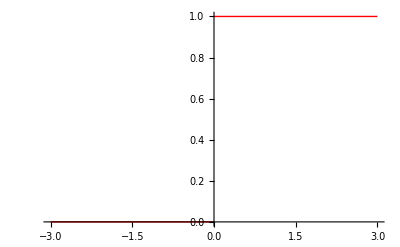

```mathematica
Plot[x,{x,-3,3},PlotStyle->{Red,Thick}]
```

## Dérivée de Heaviside Theta

```mathematica
Plot[x,{x,-3,3},PlotStyle->{Red,Thick}]
```

-Graphics-

```mathematica
Δx:=2
```

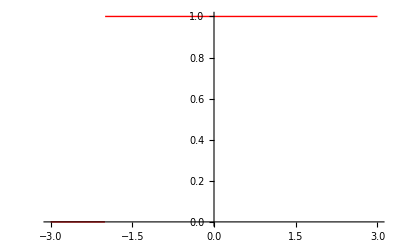

```mathematica
Plot[x+Δx,{x,-3,3},PlotStyle->{Red,Thick}]
```

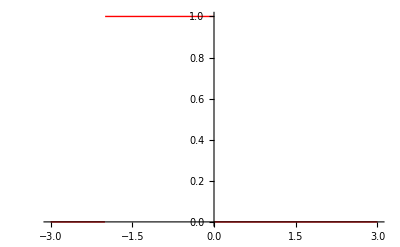

```mathematica
Plot[x+Δx-x,{x,-3,3},PlotStyle->{Red,Thick}]
```

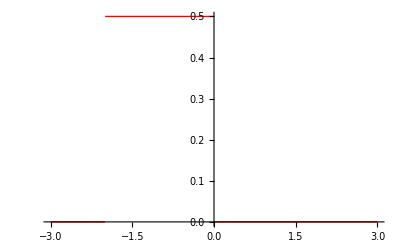

```mathematica
Plot[(x+Δx-x)/Δx,{x,-3,3},PlotStyle->{Red,Thick}]
```

```mathematica
Δx:=0.1
```

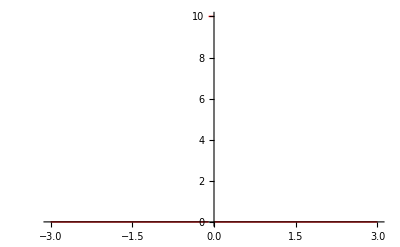

```mathematica
Plot[(x+Δx-x)/Δx,{x,-3,3},PlotStyle->{Red,Thick}]
```

```mathematica
Clear[Δx]
```

```mathematica
Limit[(x+Δx-x)/Δx,Δx->0]
```

0

```mathematica
D[x,x]
```

DiracDelta[x]

```mathematica
FourierTransform[HeavisideTheta[y],y,x]
```

ⅈ/(√(2 π) x)+√(π/2) DiracDelta[x]

```mathematica
LaplaceTransform[HeavisideTheta[x], x, s]
```

1/s